```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Documents/Tesi/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[1]}->{V[1]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "/home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing,NoLightFHCoupling}, ExcludeParticles-> {}];
```

```mathematica
process={V[1]}->{V[1]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts-3.11/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {/home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish} initialized

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 15 Particles insertions

Restoring 48 field point(s)

in total: 17 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

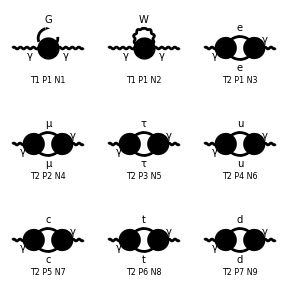

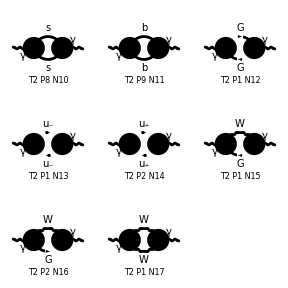

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/BGFSE/feynArts_amplitudes/OneLoopAmplitudes.m

```mathematica
FullForm[myAmp1L[[1]]]
```

Times[Complex[0,Rational[1,16]],Power[EL,2],gFFAA,Power[Pi,-4],FeynAmpDenominator[PropagatorDenominator[FourMomentum[Internal,1],MW]],MetricTensor[Index[Lorentz,1],Index[Lorentz,2]],PolarizationVector[V[1],FourMomentum[Incoming,1],Index[Lorentz,1]],Conjugate[PolarizationVector][V[1],FourMomentum[Outgoing,1],Index[Lorentz,2]]]

## Longitudinal and Transverse Part

### Projectors

```mathematica
l[Lor1_,Lor2_]=-SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1]
```

-(SP[p1,{Lor1}] SP[p1,{Lor2}])/SP[p1,p1]

```mathematica
t[Lor1_,Lor2_]=(-SP[{Lor1},{Lor2}]+SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1])/(d-1)
```

((SP[p1,{Lor1}] SP[p1,{Lor2}])/SP[p1,p1]-SP[{Lor1},{Lor2}])/(-1+d)

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[1],p_,List[i_]]->1,Conjugate[PolarizationVector][V[1],p_,List[i_]]->1}
```

{ep[V[1],p1,{Lor1}]→1,ep^*[V[1],p2,{Lor2}]→1}

```mathematica
SP[p1,p1]
```

SP[p1,p1]

```mathematica
AmpSquare[SP[{Lor1},p1],SP[{Lor1},p1]]
```

0

## Interference

```mathematica
myAmp1LABISS=Map[AmpSquare[#,1]&,myAmp1L]//FullForm
```

List[Times[Complex[0,Rational[1,16]],Power[EL,2],gFFAA,Power[Pi,-4],KiraPropagator[q1,MW],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Plus[Times[Complex[0,Rational[1,8]],Power[EL,2],gWWAA,Power[Pi,-4],KiraPropagator[q1,MW],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,8]],d,Power[EL,2],gWWAA,Power[Pi,-4],KiraPropagator[q1,MW],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ME],KiraPropagator[Plus[Times[-1,p2],q1],ME],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ME],KiraPropagator[Plus[Times[-1,p2],q1],ME],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,2]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ME],KiraPropagator[Plus[Times[-1,p2],q1],ME],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAl,2],Power[ME,2],Power[Pi,-4],KiraPropagator[q1,ME],KiraPropagator[Plus[Times[-1,p2],q1],ME],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ME],KiraPropagator[Plus[Times[-1,p2],q1],ME],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ME],KiraPropagator[Plus[Times[-1,p2],q1],ME],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,MM],KiraPropagator[Plus[Times[-1,p2],q1],MM],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,MM],KiraPropagator[Plus[Times[-1,p2],q1],MM],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,2]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,MM],KiraPropagator[Plus[Times[-1,p2],q1],MM],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAl,2],Power[MM,2],Power[Pi,-4],KiraPropagator[q1,MM],KiraPropagator[Plus[Times[-1,p2],q1],MM],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,MM],KiraPropagator[Plus[Times[-1,p2],q1],MM],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,MM],KiraPropagator[Plus[Times[-1,p2],q1],MM],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ML],KiraPropagator[Plus[Times[-1,p2],q1],ML],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ML],KiraPropagator[Plus[Times[-1,p2],q1],ML],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,2]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ML],KiraPropagator[Plus[Times[-1,p2],q1],ML],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAl,2],Power[ML,2],Power[Pi,-4],KiraPropagator[q1,ML],KiraPropagator[Plus[Times[-1,p2],q1],ML],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ML],KiraPropagator[Plus[Times[-1,p2],q1],ML],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAl,2],Power[Pi,-4],KiraPropagator[q1,ML],KiraPropagator[Plus[Times[-1,p2],q1],ML],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MU],KiraPropagator[Plus[Times[-1,p2],q1],MU],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MU],KiraPropagator[Plus[Times[-1,p2],q1],MU],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,2]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MU],KiraPropagator[Plus[Times[-1,p2],q1],MU],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAu,2],Power[MU,2],Power[Pi,-4],KiraPropagator[q1,MU],KiraPropagator[Plus[Times[-1,p2],q1],MU],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MU],KiraPropagator[Plus[Times[-1,p2],q1],MU],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MU],KiraPropagator[Plus[Times[-1,p2],q1],MU],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MC],KiraPropagator[Plus[Times[-1,p2],q1],MC],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MC],KiraPropagator[Plus[Times[-1,p2],q1],MC],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,2]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MC],KiraPropagator[Plus[Times[-1,p2],q1],MC],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAu,2],Power[MC,2],Power[Pi,-4],KiraPropagator[q1,MC],KiraPropagator[Plus[Times[-1,p2],q1],MC],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MC],KiraPropagator[Plus[Times[-1,p2],q1],MC],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MC],KiraPropagator[Plus[Times[-1,p2],q1],MC],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MT],KiraPropagator[Plus[Times[-1,p2],q1],MT],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MT],KiraPropagator[Plus[Times[-1,p2],q1],MT],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,2]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MT],KiraPropagator[Plus[Times[-1,p2],q1],MT],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAu,2],Power[MT,2],Power[Pi,-4],KiraPropagator[q1,MT],KiraPropagator[Plus[Times[-1,p2],q1],MT],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MT],KiraPropagator[Plus[Times[-1,p2],q1],MT],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAu,2],Power[Pi,-4],KiraPropagator[q1,MT],KiraPropagator[Plus[Times[-1,p2],q1],MT],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MD],KiraPropagator[Plus[Times[-1,p2],q1],MD],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MD],KiraPropagator[Plus[Times[-1,p2],q1],MD],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,2]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MD],KiraPropagator[Plus[Times[-1,p2],q1],MD],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAd,2],Power[MD,2],Power[Pi,-4],KiraPropagator[q1,MD],KiraPropagator[Plus[Times[-1,p2],q1],MD],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MD],KiraPropagator[Plus[Times[-1,p2],q1],MD],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MD],KiraPropagator[Plus[Times[-1,p2],q1],MD],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MS],KiraPropagator[Plus[Times[-1,p2],q1],MS],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MS],KiraPropagator[Plus[Times[-1,p2],q1],MS],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,2]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MS],KiraPropagator[Plus[Times[-1,p2],q1],MS],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAd,2],Power[MS,2],Power[Pi,-4],KiraPropagator[q1,MS],KiraPropagator[Plus[Times[-1,p2],q1],MS],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MS],KiraPropagator[Plus[Times[-1,p2],q1],MS],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MS],KiraPropagator[Plus[Times[-1,p2],q1],MS],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MB],KiraPropagator[Plus[Times[-1,p2],q1],MB],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MB],KiraPropagator[Plus[Times[-1,p2],q1],MB],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,2]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MB],KiraPropagator[Plus[Times[-1,p2],q1],MB],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAd,2],Power[MB,2],Power[Pi,-4],KiraPropagator[q1,MB],KiraPropagator[Plus[Times[-1,p2],q1],MB],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MB],KiraPropagator[Plus[Times[-1,p2],q1],MB],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gAd,2],Power[Pi,-4],KiraPropagator[q1,MB],KiraPropagator[Plus[Times[-1,p2],q1],MB],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],SumOver[Index[Colour,3],3],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,16]],Power[EL,2],Power[gFFA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[p2,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,8]],Power[EL,2],Power[gFFA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,8]],Power[EL,2],Power[gFFA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],Power[EL,2],Power[gFFA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,16]],Power[EL,2],Power[ggmgmA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,16]],Power[EL,2],Power[ggmgmA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Plus[Times[Complex[0,Rational[-1,16]],Power[EL,2],Power[ggpgpA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,16]],Power[EL,2],Power[ggpgpA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]],Times[Complex[0,Rational[1,16]],Power[EL,2],Power[gFAW,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,16]],Power[EL,2],Power[gFAW,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Plus[Times[Complex[0,Rational[3,16]],Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p1,List[Lor2]],SP[p2,List[Lor1]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[3,16]],Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[p2,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,16]],d,Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[p2,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-3,16]],Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,8]],d,Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor2]],SP[q1,List[Lor1]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-3,16]],Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,8]],d,Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[3,8]],Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,4]],d,Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,List[Lor1]],SP[q1,List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-5,16]],Power[EL,2],Power[gWWA,2],Power[Pi,-4],psm,KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[1,8]],Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[p2,q1],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]],Times[Complex[0,Rational[-1,8]],Power[EL,2],Power[gWWA,2],Power[Pi,-4],KiraPropagator[q1,MW],KiraPropagator[Plus[Times[-1,p2],q1],MW],PolarizationVector[V[1],p1,List[Lor1]],SP[q1,q1],SP[List[Lor1],List[Lor2]],Conjugate[PolarizationVector][V[1],p2,List[Lor2]]]]]

```mathematica
myAmp1LnoEP=myAmp1LABISS/.removePolarizationVectors
```

{(ⅈ EL^2 gFFAA KiraPropagator[q1,MW] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}])/(16 π^4),(ⅈ EL^2 gWWAA KiraPropagator[q1,MW] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}])/(8 π^4)-(ⅈ d EL^2 gWWAA KiraPropagator[q1,MW] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}])/(8 π^4),-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ME] KiraPropagator[-p2+q1,ME] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ME] KiraPropagator[-p2+q1,ME] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(2 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ME] KiraPropagator[-p2+q1,ME] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAl^2 ME^2 KiraPropagator[q1,ME] KiraPropagator[-p2+q1,ME] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ME] KiraPropagator[-p2+q1,ME] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ME] KiraPropagator[-p2+q1,ME] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}],-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,MM] KiraPropagator[-p2+q1,MM] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,MM] KiraPropagator[-p2+q1,MM] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(2 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,MM] KiraPropagator[-p2+q1,MM] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAl^2 MM^2 KiraPropagator[q1,MM] KiraPropagator[-p2+q1,MM] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,MM] KiraPropagator[-p2+q1,MM] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,MM] KiraPropagator[-p2+q1,MM] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}],-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ML] KiraPropagator[-p2+q1,ML] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ML] KiraPropagator[-p2+q1,ML] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(2 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ML] KiraPropagator[-p2+q1,ML] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAl^2 ML^2 KiraPropagator[q1,ML] KiraPropagator[-p2+q1,ML] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ML] KiraPropagator[-p2+q1,ML] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ML] KiraPropagator[-p2+q1,ML] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}],-1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MU] KiraPropagator[-p2+q1,MU] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MU] KiraPropagator[-p2+q1,MU] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(2 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MU] KiraPropagator[-p2+q1,MU] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAu^2 MU^2 KiraPropagator[q1,MU] KiraPropagator[-p2+q1,MU] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MU] KiraPropagator[-p2+q1,MU] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MU] KiraPropagator[-p2+q1,MU] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}],-1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MC] KiraPropagator[-p2+q1,MC] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MC] KiraPropagator[-p2+q1,MC] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(2 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MC] KiraPropagator[-p2+q1,MC] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAu^2 MC^2 KiraPropagator[q1,MC] KiraPropagator[-p2+q1,MC] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MC] KiraPropagator[-p2+q1,MC] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MC] KiraPropagator[-p2+q1,MC] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}],-1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MT] KiraPropagator[-p2+q1,MT] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MT] KiraPropagator[-p2+q1,MT] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(2 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MT] KiraPropagator[-p2+q1,MT] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAu^2 MT^2 KiraPropagator[q1,MT] KiraPropagator[-p2+q1,MT] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MT] KiraPropagator[-p2+q1,MT] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAu^2 KiraPropagator[q1,MT] KiraPropagator[-p2+q1,MT] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}],-1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MD] KiraPropagator[-p2+q1,MD] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MD] KiraPropagator[-p2+q1,MD] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(2 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MD] KiraPropagator[-p2+q1,MD] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAd^2 MD^2 KiraPropagator[q1,MD] KiraPropagator[-p2+q1,MD] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MD] KiraPropagator[-p2+q1,MD] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MD] KiraPropagator[-p2+q1,MD] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}],-1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MS] KiraPropagator[-p2+q1,MS] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MS] KiraPropagator[-p2+q1,MS] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(2 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MS] KiraPropagator[-p2+q1,MS] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAd^2 MS^2 KiraPropagator[q1,MS] KiraPropagator[-p2+q1,MS] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MS] KiraPropagator[-p2+q1,MS] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MS] KiraPropagator[-p2+q1,MS] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}],-1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MB] KiraPropagator[-p2+q1,MB] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MB] KiraPropagator[-p2+q1,MB] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(2 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MB] KiraPropagator[-p2+q1,MB] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAd^2 MB^2 KiraPropagator[q1,MB] KiraPropagator[-p2+q1,MB] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]+1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MB] KiraPropagator[-p2+q1,MB] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gAd^2 KiraPropagator[q1,MB] KiraPropagator[-p2+q1,MB] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] SumOver[Col3,3] ep^*[V[1],p2,{Lor2}],-1/(16 π^4)ⅈ EL^2 gFFA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[p2,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(8 π^4)ⅈ EL^2 gFFA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] ep^*[V[1],p2,{Lor2}]+1/(8 π^4)ⅈ EL^2 gFFA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ EL^2 gFFA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}],-1/(16 π^4)ⅈ EL^2 ggmgmA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(16 π^4)ⅈ EL^2 ggmgmA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}],-1/(16 π^4)ⅈ EL^2 ggpgpA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(16 π^4)ⅈ EL^2 ggpgpA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}],1/(16 π^4)ⅈ EL^2 gFAW^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}],1/(16 π^4)ⅈ EL^2 gFAW^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}],1/(16 π^4)3 ⅈ EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p1,{Lor2}] SP[p2,{Lor1}] ep^*[V[1],p2,{Lor2}]+1/(16 π^4)3 ⅈ EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[p2,{Lor2}] ep^*[V[1],p2,{Lor2}]-1/(16 π^4)ⅈ d EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[p2,{Lor2}] ep^*[V[1],p2,{Lor2}]-1/(16 π^4)3 ⅈ EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] ep^*[V[1],p2,{Lor2}]+1/(8 π^4)ⅈ d EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor2}] SP[q1,{Lor1}] ep^*[V[1],p2,{Lor2}]-1/(16 π^4)3 ⅈ EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(8 π^4)ⅈ d EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(8 π^4)3 ⅈ EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]-1/(4 π^4)ⅈ d EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[q1,{Lor1}] SP[q1,{Lor2}] ep^*[V[1],p2,{Lor2}]-1/(16 π^4)5 ⅈ EL^2 gWWA^2 psm KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]+1/(8 π^4)ⅈ EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[p2,q1] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]-1/(8 π^4)ⅈ EL^2 gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ep[V[1],p1,{Lor1}] SP[q1,q1] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]}

```mathematica
myAmp1LLongitudinal=Map[AmpSquare[#*l[Lor1,Lor2],1]&,myAmp1LnoEP];
```

```mathematica
myAmp1LTransverse=Map[AmpSquare[#*t[Lor1,Lor2],1]&,myAmp1LnoEP];
```

```mathematica
SquareSimplifyAndSave[myAmp1LnoEP*l[Lor1,Lor2],{1}]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_3_1.m.

Computed contribution 4-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_4_1.m.

Computed contribution 5-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_5_1.m.

Computed contribution 6-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_6_1.m.

Computed contribution 7-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_7_1.m.

Computed contribution 8-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_8_1.m.

Computed contribution 9-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_9_1.m.

Computed contribution 10-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_10_1.m.

Computed contribution 11-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_11_1.m.

Computed contribution 12-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_12_1.m.

Computed contribution 13-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_13_1.m.

Computed contribution 14-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_14_1.m.

Computed contribution 15-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_15_1.m.

Computed contribution 16-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_16_1.m.

Computed contribution 17-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_17_1.m.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/kinematics.m.

```mathematica
ExtractFamily[test]
```

{A0,{MW}}

```mathematica
ExtractFamily[test1]
```

{A0,{MW}}

```mathematica
ExtractFamily[test2]
```

{A0,{ME}}

```mathematica
ExtractFamily[test3]
```

{A0,{MM}}

```mathematica
ExtractFamily[test4]
```

{A0,{ML}}

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,17},{j,1}]
```

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_1_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_2_1.m.

Integral family {A0, {ME}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_3_1.m.

Integral family {A0, {MM}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_4_1.m.

Integral family {A0, {ML}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_5_1.m.

Integral family {A0, {MU}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_6_1.m.

Integral family {A0, {MC}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_7_1.m.

Integral family {A0, {MT}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_8_1.m.

Integral family {A0, {MD}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_9_1.m.

Integral family {A0, {MS}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_10_1.m.

Integral family {A0, {MB}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_11_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_12_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_13_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_14_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_15_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_16_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_17_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,17},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_6_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_7_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_8_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_9_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_10_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_11_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_12_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_13_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_14_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_15_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_16_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_17_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},-1,1],userIntegral[A0,{ME},0,0],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,-1],userIntegral[A0,{ME},1,0],userIntegral[A0,{MM},-1,1],userIntegral[A0,{MM},0,0],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,-1],userIntegral[A0,{MM},1,0],userIntegral[A0,{ML},-1,1],userIntegral[A0,{ML},0,0],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,-1],userIntegral[A0,{ML},1,0],userIntegral[A0,{MU},-1,1],userIntegral[A0,{MU},0,0],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,-1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MC},-1,1],userIntegral[A0,{MC},0,0],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,-1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MT},-1,1],userIntegral[A0,{MT},0,0],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,-1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MD},-1,1],userIntegral[A0,{MD},0,0],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,-1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MS},-1,1],userIntegral[A0,{MS},0,0],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,-1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MB},-1,1],userIntegral[A0,{MB},0,0],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,-1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MW},-1,1],userIntegral[A0,{MW},0,0],userIntegral[A0,{MW},1,-1],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
PrintRules[]
```

{}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,17},{j,1}]
```